Dynamic simulation of three-wheeled omnidirectional mobile robot

```mathematica
Clear["Global`*"];
```

## Section I.

### Configuration definition

#### Global coordinate system definition

```mathematica
ux={1,0,0};
uy={0,1,0};
uz={0,0,1};
rO={0,0,0};
```

#### Basic coordinate system definition

```mathematica
φA=π/6; φB=φA+(2π)/3;φC=φB+(2π)/3;
```

```mathematica
uxA=RotationMatrix[φA,{0,0,1}].ux;
uxB=RotationMatrix[φB,{0,0,1}].ux;
uxC=RotationMatrix[φC,{0,0,1}].ux;
uyA=RotationMatrix[φA,{0,0,1}].uy;
uyB=RotationMatrix[φB,{0,0,1}].uy;
uyC=RotationMatrix[φC,{0,0,1}].uy;
uzA=Cross[uxA,uyA];
uzB=Cross[uxB,uyB];
uzC=Cross[uxC,uyC];
```

### Geometry parameters

#### Wheel definition

```mathematica
wheelCircleRadius=0.12;
wheelRadius=0.03;
wheelWidth=0.0050;
massWheel=0.06;
A=({{-Sin[φA], Cos[φA], wheelCircleRadius}, {-Sin[φB], Cos[φB], wheelCircleRadius}, {-Sin[φC], Cos[φC], wheelCircleRadius}});
```

```mathematica
rA=wheelCircleRadius uxA;
rB=wheelCircleRadius uxB;
rC=wheelCircleRadius uxC;
wheelθMeasured = 0.0390;
```

#### Case definition

```mathematica
ρ=1000;
offsetLength=0.04;
wheelCircleRadiusRatio =0.8;
dummyCaseRadius=wheelCircleRadiusRatio wheelCircleRadius;
dummyCaseHeight=0.05;
rCase={0,0,offsetLength}
mCase=dummyCaseRadius^2 π dummyCaseHeight ρ
cmCase = rCase + {0,0,dummyCaseHeight/2}
```

{0,0,0.04}

1.44765

{0,0,0.065}

#### Package definition

```mathematica
packageHeight = 0.5;
packageRadius=0.3 dummyCaseRadius;
cmPackage={0,0,dummyCaseHeight/2+packageHeight/2};
mPackage=packageRadius^2 π packageHeight ρ
```

1.30288

#### Common mass center

```mathematica
cmC=cmCase;
cmC=(cmCase mCase+cmPackage mPackage)/(mCase+mPackage)
```

{0.,0.,0.164474}

### 3 D model of the robot and its environment

#### Draw functions

```mathematica
TranslateAndRotate[g_,x_,y_,α_]:=Module[{},Rotate[Translate[g,{x,y}],α,{x,y}]]
```

```mathematica
textOffset = 0.02;fontSize=16;
RobotCaseGraphics3D={
Red,
Sphere[rO,wheelCircleRadius/50],Text[Style["r_O",FontSize->fontSize],rO - ux textOffset],
Sphere[rCase,wheelCircleRadius/50],Text[Style["r_Case",FontSize->fontSize],rCase + ux textOffset+ uz textOffset],
Sphere[rA,wheelCircleRadius/50],Text[Style["r_A",FontSize->fontSize],rA - ux textOffset],
Sphere[rB,wheelCircleRadius/50],Text[Style["r_B",FontSize->fontSize],rB - ux textOffset],
Sphere[rC,wheelCircleRadius/50],Text[Style["r_C",FontSize->fontSize],rC - ux textOffset],
Pink,
Sphere[cmCase,wheelCircleRadius/50],(*Text[Style["cmCase",FontSize->fontSize],cmCase - ux textOffset],*)
Sphere[cmPackage,wheelCircleRadius/50],(*Text[Style["cmPackage",FontSize->fontSize],cmPackage - ux textOffset],*)
Sphere[cmC,wheelCircleRadius/50],(*Text[Style["cmC",FontSize->fontSize],cmC - ux textOffset],*)
Gray,Opacity[0.1],
Cylinder[{rA-wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0}),rA+wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0})},wheelRadius],
Cylinder[{rB-wheelWidth/2 (Normalize[rB][[1;;2]]~Join~{0}),rB+wheelWidth/2 (Normalize[rB][[1;;2]]~Join~{0})},wheelRadius],
Cylinder[{rC-wheelWidth/2 (Normalize[rC][[1;;2]]~Join~{0}),rC+wheelWidth/2 (Normalize[rC][[1;;2]]~Join~{0})},wheelRadius],
Black,Thick,Opacity[1],
	(*Line[{wheelCircleRadiusRatio rA,rA}],*)
	Line[{ rA, rA+offsetLength uz}],Line[{rCase, rA+offsetLength uz}],
	Line[{ rB, rB+offsetLength uz}],Line[{rCase, rB+offsetLength uz}],
	Line[{ rC, rC+offsetLength uz}],Line[{rCase, rC+offsetLength uz}],
Cyan,Opacity[0.6],
Cylinder[{rCase,rCase+dummyCaseHeight uz},dummyCaseRadius],
Black,Opacity[0.2],EdgeForm[White],
Cylinder[{rCase+dummyCaseHeight uz,rCase+dummyCaseHeight uz+packageHeight uz},packageRadius]
};
```

```mathematica
DrawRobot3D[{x_,y_,z_,α_}]:={EdgeForm[Black],Rotate[Translate[RobotCaseGraphics3D,{x,y,z}],α,{0,0,1}]}
```

```mathematica
DrawGround={EdgeForm[Black],
planeSize=10 wheelCircleRadius;
Black,Opacity[0.1],Polygon[{{-planeSize wheelCircleRadius,-planeSize wheelCircleRadius,-wheelRadius},{-planeSize wheelCircleRadius,planeSize wheelCircleRadius,-wheelRadius},{planeSize wheelCircleRadius,planeSize wheelCircleRadius,-wheelRadius},{planeSize wheelCircleRadius,-planeSize  wheelCircleRadius,-wheelRadius}}]
};
```

```mathematica
DrawGlobalAxes[{x_,y_,z_,φ_}]:={EdgeForm[Black],
Translate[
{
Black,
	Line[{rO,ux planeSize/13}],Text[Style["x",FontSize->fontSize],1.2ux planeSize/13],
	Line[{rO,uy planeSize/13}],Text[Style["y",FontSize->fontSize],1.2uy planeSize/13],
	Line[{rO,uz planeSize/13}],Text[Style["z",FontSize->fontSize],1.2uz planeSize/13],

},{x,y,z}]}
```

#### Draw 3D graphics

```mathematica
DrawRobot3D[{0,0,0,π/9}]//Graphics3D
```

```mathematica
initialPos={0,0,0,0};
Graphics3D[
DrawRobot3D[initialPos]~Join~DrawGlobalAxes[initialPos]~Join~DrawGround,
AxesLabel->{x,y,z},Axes->{True, True, True}]
```

-Graphics3D-

### Free Body Diagrams

#### Draw functions

```mathematica
fontSize = 16;
aVectorEnd = 0.2 wheelCircleRadius; aVectorText = 0.3 wheelCircleRadius; 
ϵVectorEnd = 0.15 wheelCircleRadius; ϵVectorText = 0.2 wheelCircleRadius; 
GVectorEnd= 0.15 wheelCircleRadius;GVectorText= 0.17 wheelCircleRadius;
KVectorEnd= 0.15 wheelCircleRadius;KVectorText= 0.25 wheelCircleRadius;
wheelPositionText = 0.006;
vThick=wheelCircleRadius/20;
vArrHead=0.12 wheelCircleRadius;
DrawCaseFBD={
Red,Sphere[rO,wheelCircleRadius/100],
Gray,Thickness[vThick/5],Arrowheads[vArrHead],
	Line[{rO,ux wheelCircleRadius}],Text[Style[x,FontSize->fontSize],1.1ux wheelCircleRadius],
	Line[{rO,uy wheelCircleRadius}],Text[Style[y,FontSize->fontSize],1.1uy wheelCircleRadius],
	Line[{rO,uz wheelCircleRadius}],Text[Style[z,FontSize->fontSize],1.1uz wheelCircleRadius],
Black,Thickness[vThick],Arrowheads[vArrHead],
	Line[{rCase,rA+offsetLength uz}],Line[{rA,rA+offsetLength uz}],
	Line[{rCase,rB+offsetLength uz}],Line[{rB,rB+offsetLength uz}],
	Line[{rCase,rC+offsetLength uz}],Line[{rC,rC+offsetLength uz}],
Blue,Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{rCase,rCase-GVectorEnd uz}],Text[Style["G",FontSize->16],rCase-GVectorText uz+GVectorText/4 ux+GVectorText/4 uy],
	Arrow[{rA-KVectorEnd ux,rA}],Text[Style["K_x^A",FontSize->fontSize],rA-KVectorText ux],
	Arrow[{rA-KVectorEnd uy,rA}],Text[Style["K_y^A",FontSize->fontSize],rA-KVectorText uy],
	Arrow[{rA-KVectorEnd uz,rA}],Text[Style["K_z^A",FontSize->fontSize],rA-KVectorText uz],
	Arrow[{rB-KVectorEnd ux,rB}],Text[Style["K_x^B",FontSize->fontSize],rB-KVectorText ux],
	Arrow[{rB-KVectorEnd uy,rB}],Text[Style["K_y^B",FontSize->fontSize],rB-KVectorText uy],
	Arrow[{rB-KVectorEnd uz,rB}],Text[Style["K_z^B",FontSize->fontSize],rB-KVectorText uz],
	Arrow[{rC-KVectorEnd ux,rC}],Text[Style["K_x^C",FontSize->fontSize],rC-KVectorText ux],
	Arrow[{rC-KVectorEnd uy,rC}],Text[Style["K_y^C",FontSize->fontSize],rC-KVectorText uy],
	Arrow[{rC-KVectorEnd uz,rC}],Text[Style["K_z^C",FontSize->fontSize],rC-KVectorText uz],
Red,
Thickness[1.2 vThick],Arrowheads[1.2 vArrHead],
	Arrow[{rCase,rCase+aVectorEnd ux}],Text[Style["a_x",FontSize->fontSize],rCase+aVectorText ux],
	Arrow[{rCase,rCase+aVectorEnd uy}],Text[Style["a_y",FontSize->fontSize],rCase+aVectorText uy],
	Arrow[{rCase,rCase+aVectorEnd uz}],Text[Style["a_z",FontSize->fontSize],rCase+aVectorText uz],
Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{rO,rO+ϵVectorEnd ux}],Text[Style["ϵ_x",FontSize->fontSize],rO+ϵVectorText ux],
	Arrow[{rO,rO+ϵVectorEnd uy}],Text[Style["ϵ_y",FontSize->fontSize],rO+ϵVectorText uy],
	Arrow[{rO,rO+ϵVectorEnd uz}],Text[Style["ϵ_z",FontSize->fontSize],rO+ϵVectorText uz-ϵVectorText/4 ux-ϵVectorText/4 uy],
Brown,Text[Style["r_A",FontSize->16],rA+wheelPositionText ux+wheelPositionText uy],
Brown,Text[Style["r_B",FontSize->16],rB+wheelPositionText ux+wheelPositionText uy],
Brown,Text[Style["r_C",FontSize->16],rC+wheelPositionText ux+wheelPositionText uy],
Brown,Text[Style["r_O",FontSize->16],rO-wheelPositionText ux-wheelPositionText uy],
Brown,Text[Style["r_Case",FontSize->16],rCase-3 wheelPositionText ux-2 wheelPositionText uy],
};

DrawAccelerationState[ax_,ay_,ϵz_,MA_,MB_,MC_,nA_,nB_,nC_]:={
M1=wheelCircleRadius;
M2=wheelCircleRadius;
accv=M1 {ax,ay,ϵz/20};
axy=N[√(ax^2+ay^2)];
Mv=-M2 {MA,MB,MC};
Red,Sphere[rO,wheelCircleRadius/100],
Blue,Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{rA,rA+Mv⟦1⟧ uyA}],Text["M_A="<>ToString[NumberForm[MA,{6,2}]]<>"[Nm]"<>"\n"<>"n_A="<>ToString[NumberForm[nA,{6,2}]]<>"[N]",rA+wheelCircleRadius uxA],
	Arrow[{rB,rB+Mv⟦2⟧  uyB}],Text["M_B="<>ToString[NumberForm[MB,{6,2}]]<>"[Nm]"<>"\n"<>"n_B="<>ToString[NumberForm[nB,{6,2}]]<>"[N]",rB+wheelCircleRadius uxB],
	Arrow[{rC,rC+Mv⟦3⟧  uyC}],Text["M_C="<>ToString[NumberForm[MC,{6,2}]]<>"[Nm]"<>"\n"<>"n_C="<>ToString[NumberForm[nC,{6,2}]]<>"[N]",rC+wheelCircleRadius uxC],
Red,
Thickness[vThick],Arrowheads[vArrHead],
	If[ϵz≠0,{Arrow[{rO,rO+ accv⟦3⟧ uz}],Text["ϵ_z="<>ToString[NumberForm[ϵz,{6,2}]]<>"[s^-2]",1.2(rO+ accv⟦3⟧ uz)]},],
Thickness[vThick],Arrowheads[1.2 vArrHead],
	(*If[ax≠0,{Arrow[{rO,rO+ accv⟦1⟧ ux}],Text["a_x="<>ToString[ax]<>"[m s^-2]",1.2(rO+ accv⟦1⟧ ux)]},],
	If[ay≠0,{Arrow[{rO,rO+ accv⟦2⟧ uy}],Text["a_y="<>ToString[ay]<>"[m s^-2]",1.2(rO+ accv⟦2⟧ uy)]},],*)
If[ay≠0||ax≠0,{Arrow[{cmC,cmC+ accv⟦2⟧ uy+ accv⟦1⟧ ux}],Text["a_xy="<>ToString[NumberForm[axy,{6,2}]]<>"[m s^-2]",1.2(cmC+ accv⟦2⟧ uy+ accv⟦1⟧ ux)]},],
};
```

```mathematica
fontSize = 14;
aVectorEnd = 0.7 wheelCircleRadius; aVectorText = 0.8 wheelCircleRadius; 
ϵVectorStart= 1.0wheelCircleRadius; ϵVectorEnd = 1.15 wheelCircleRadius; ϵVectorText = 1.3 wheelCircleRadius; 
GVectorEnd= 0.15 wheelCircleRadius;GVectorText= 0.17 wheelCircleRadius;
KVectorEnd= 0.3 wheelCircleRadius;KVectorText= 0.35 wheelCircleRadius;
SVectorEnd= 0.3 wheelCircleRadius;SVectorText= 0.35 wheelCircleRadius;
NVectorEnd= 0.3 wheelCircleRadius;NVectorText= 0.35 wheelCircleRadius;
axisLength = wheelCircleRadius 2;
wheelPositionText = 0.006;
vThick=wheelCircleRadius/20;
vArrHead=0.12 wheelCircleRadius;
DrawWheelsFBD={
Red,Sphere[rA,wheelCircleRadius/50],
Gray,
	Line[{rA,rA+uxA axisLength}],Text[Style["x_A",FontSize->fontSize],1.1(rA+uxA axisLength)],
	Line[{rA,rA+uyA axisLength}],Text[Style["y_A",FontSize->fontSize],1.1(rA+uyA axisLength)],
	Line[{rA,rA+uzA axisLength}],Text[Style["z_A",FontSize->fontSize],1.1(rA+uzA axisLength)],
	Line[{rB,rB+uxB axisLength}],Text[Style["x_B",FontSize->fontSize],1.1(rB+uxB axisLength)],
	Line[{rB,rB+uyB axisLength}],Text[Style["y_B",FontSize->fontSize],1.1(rB+uyB axisLength)],
	Line[{rB,rB+uzB axisLength}],Text[Style["z_B",FontSize->fontSize],1.1(rB+uzB axisLength)],
	Line[{rC,rC+uxC axisLength}],Text[Style["x_C",FontSize->fontSize],1.1(rC+uxC axisLength)],
	Line[{rC,rC+uyC axisLength}],Text[Style["y_C",FontSize->fontSize],1.1(rC+uyC axisLength)],
	Line[{rC,rC+uzC axisLength}],Text[Style["z_C",FontSize->fontSize],1.1(rC+uzC axisLength)],
Red,Thickness[0.5 vThick],Arrowheads[0.5vArrHead],
	Arrow[{rA+ϵVectorStart uxA,rA+ϵVectorEnd uxA}],Text[Style["ϵ_x^A",FontSize->fontSize],rA+ϵVectorText uxA],
	Arrow[{rA+ϵVectorStart uyA,rA+ϵVectorEnd uyA}],Text[Style["ϵ_y^A",FontSize->fontSize],rA+ϵVectorText uyA],
	Arrow[{rA+ϵVectorStart uzA,rA+ϵVectorEnd uzA}],Text[Style["ϵ_z^A",FontSize->fontSize],rA+ϵVectorText uzA],
	Arrow[{rB+ϵVectorStart uxB,rB+ϵVectorEnd uxB}],Text[Style["ϵ_x^B",FontSize->fontSize],rB+ϵVectorText uxB],
	Arrow[{rB+ϵVectorStart uyB,rB+ϵVectorEnd uyB}],Text[Style["ϵ_y^B",FontSize->fontSize],rB+ϵVectorText uyB],
	Arrow[{rB+ϵVectorStart uzB,rB+ϵVectorEnd uzB}],Text[Style["ϵ_z^B",FontSize->fontSize],rB+ϵVectorText uzB],
	Arrow[{rC+ϵVectorStart uxC,rC+ϵVectorEnd uxC}],Text[Style["ϵ_x^C",FontSize->fontSize],rC+ϵVectorText uxC],
	Arrow[{rC+ϵVectorStart uyC,rC+ϵVectorEnd uyC}],Text[Style["ϵ_y^C",FontSize->fontSize],rC+ϵVectorText uyC],
	Arrow[{rC+ϵVectorStart uzC,rC+ϵVectorEnd uzC}],Text[Style["ϵ_z^C",FontSize->fontSize],rC+ϵVectorText uzC],
Red,Thickness[0.5 vThick],Arrowheads[0.5vArrHead],
	Arrow[{rA,rA+aVectorEnd uxA}],Text[Style["a_x^A",FontSize->fontSize],rA+aVectorText uxA],
	Arrow[{rA,rA+aVectorEnd uyA}],Text[Style["a_y^A",FontSize->fontSize],rA+aVectorText uyA],
	Arrow[{rA,rA+aVectorEnd uzA}],Text[Style["a_z^A",FontSize->fontSize],rA+aVectorText uzA],
	Arrow[{rB,rB+aVectorEnd uxB}],Text[Style["a_x^B",FontSize->fontSize],rB+aVectorText uxB],
	Arrow[{rB,rB+aVectorEnd uyB}],Text[Style["a_y^B",FontSize->fontSize],rB+aVectorText uyB],
	Arrow[{rB,rB+aVectorEnd uzB}],Text[Style["a_z^B",FontSize->fontSize],rB+aVectorText uzB],
	Arrow[{rC,rC+aVectorEnd uxC}],Text[Style["a_x^C",FontSize->fontSize],rC+aVectorText uxC],
	Arrow[{rC,rC+aVectorEnd uyC}],Text[Style["a_y^C",FontSize->fontSize],rC+aVectorText uyC],
	Arrow[{rC,rC+aVectorEnd uzC}],Text[Style["a_z^C",FontSize->fontSize],rC+aVectorText uzC],
Blue,
Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{rA,rA-GVectorEnd uz}],Text[Style["G_A",FontSize->fontSize],rA-GVectorText uz],
	Arrow[{rB,rB-GVectorEnd uz}],Text[Style["G_B",FontSize->fontSize],rB-GVectorText uz],
	Arrow[{rC,rC-GVectorEnd uz}],Text[Style["G_C",FontSize->fontSize],rC-GVectorText uz],
	Arrow[{rA-{0,0,wheelRadius},rA-{0,0,wheelRadius}+SVectorEnd uyA}],Text[Style["S_A",FontSize->fontSize],1.1(rA-{0,0,wheelRadius}+SVectorEnd uyA)],
	Arrow[{rB-{0,0,wheelRadius},rB-{0,0,wheelRadius}+SVectorEnd uyB}],Text[Style["S_B",FontSize->fontSize],1.1(rB-{0,0,wheelRadius}+SVectorEnd uyB)],
	Arrow[{rC-{0,0,wheelRadius},rC-{0,0,wheelRadius}+SVectorEnd uyC}],Text[Style["S_C",FontSize->fontSize],1.1(rC-{0,0,wheelRadius}+SVectorEnd uyC)],
	Arrow[{rA-{0,0,wheelRadius}-NVectorEnd uzA,rA-{0,0,wheelRadius}}],Text[Style["N_A",FontSize->fontSize],1.1(rA-{0,0,wheelRadius}-NVectorEnd uzA)],
	Arrow[{rB-{0,0,wheelRadius}-NVectorEnd uzB,rB-{0,0,wheelRadius}}],Text[Style["N_B",FontSize->fontSize],1.1(rB-{0,0,wheelRadius}-NVectorEnd uzB)],
	Arrow[{rC-{0,0,wheelRadius}-NVectorEnd uzC,rC-{0,0,wheelRadius}}],Text[Style["N_C",FontSize->fontSize],1.1(rC-{0,0,wheelRadius}-NVectorEnd uzC)],
	Arrow[{rA+KVectorEnd uxA,rA}],Text[Style["K_x^A",FontSize->fontSize],1.1(rA+KVectorText uxA)],
	Arrow[{rA+KVectorEnd uyA,rA}],Text[Style["K_y^A",FontSize->fontSize],1.1(rA+KVectorText uyA)],
	Arrow[{rA+KVectorEnd uzA,rA}],Text[Style["K_z^A",FontSize->fontSize],1.1(rA+KVectorText uzA)],
	Arrow[{rB+KVectorEnd uxB,rB}],Text[Style["K_x^B",FontSize->fontSize],1.1(rB+KVectorText uxB)],
	Arrow[{rB+KVectorEnd uyB,rB}],Text[Style["K_y^B",FontSize->fontSize],1.1(rB+KVectorText uyB)],
	Arrow[{rB+KVectorEnd uzB,rB}],Text[Style["K_z^B",FontSize->fontSize],1.1(rB+KVectorText uzB)],
	Arrow[{rC+KVectorEnd uxC,rC}],Text[Style["K_x^C",FontSize->fontSize],1.1(rC+KVectorText uxC)],
	Arrow[{rC+KVectorEnd uyC,rC}],Text[Style["K_y^C",FontSize->fontSize],1.1(rC+KVectorText uyC)],
	Arrow[{rC+KVectorEnd uzC,rC}],Text[Style["K_z^C",FontSize->fontSize],1.1(rC+KVectorText uzC)],
Gray,Opacity[0.1],
Cylinder[{rA-wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0}),rA+wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0})},wheelRadius],
Cylinder[{rB-wheelWidth/2 (Normalize[rB][[1;;2]]~Join~{0}),rB+wheelWidth/2 (Normalize[rB][[1;;2]]~Join~{0})},wheelRadius],
Cylinder[{rC-wheelWidth/2 (Normalize[rC][[1;;2]]~Join~{0}),rC+wheelWidth/2 (Normalize[rC][[1;;2]]~Join~{0})},wheelRadius],
};
fontSize = 16;
aVectorEnd = 0.7 wheelCircleRadius; aVectorText = 0.8 wheelCircleRadius; 
ϵVectorStart= 1.0wheelCircleRadius; ϵVectorEnd = 1.15 wheelCircleRadius; ϵVectorText = 1.3 wheelCircleRadius; 
GVectorEnd= 0.15 wheelCircleRadius;GVectorText= 0.17 wheelCircleRadius;
KVectorEnd= 0.3 wheelCircleRadius;KVectorText= 0.35 wheelCircleRadius;
SVectorEnd= 0.3 wheelCircleRadius;SVectorText= 0.35 wheelCircleRadius;
NVectorEnd= 0.3 wheelCircleRadius;NVectorText= 0.35 wheelCircleRadius;
axisLength = wheelCircleRadius 1.4;
wheelPositionText = 0.02;
vThick=wheelCircleRadius/20;
vArrHead=0.2 wheelCircleRadius;
DrawWheelAFBD={
Brown,Sphere[rA,wheelCircleRadius/50],Text[Style["r_A",FontSize->fontSize],rA-uyA wheelPositionText],
Gray,
	Line[{rA,rA+uxA axisLength}],Text[Style["x_A",FontSize->fontSize],1.1(rA+uxA axisLength)],
	Line[{rA,rA+uyA axisLength}],Text[Style["y_A",FontSize->fontSize],1.1(rA+uyA axisLength)],
	Line[{rA,rA+uzA axisLength}],Text[Style["z_A",FontSize->fontSize],1.1(rA+uzA axisLength)],
Red,Thickness[0.5 vThick],Arrowheads[0.8vArrHead],
	Arrow[{rA+ϵVectorStart uxA,rA+ϵVectorEnd uxA}],Text[Style["ϵ_x^A",FontSize->fontSize],rA+ϵVectorText uxA],
	Arrow[{rA+ϵVectorStart uyA,rA+ϵVectorEnd uyA}],Text[Style["ϵ_y^A",FontSize->fontSize],rA+ϵVectorText uyA],
	Arrow[{rA+ϵVectorStart uzA,rA+ϵVectorEnd uzA}],Text[Style["ϵ_z^A",FontSize->fontSize],rA+ϵVectorText uzA],
Red,Thickness[0.5 vThick],Arrowheads[0.8vArrHead],
	Arrow[{rA,rA+aVectorEnd uxA}],Text[Style["a_x^A",FontSize->fontSize],rA+aVectorText uxA],
	Arrow[{rA,rA+aVectorEnd uyA}],Text[Style["a_y^A",FontSize->fontSize],rA+aVectorText uyA],
	Arrow[{rA,rA+aVectorEnd uzA}],Text[Style["a_z^A",FontSize->fontSize],rA+aVectorText uzA],
Blue,
Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{rA,rA-GVectorEnd uz}],Text[Style["G_A",FontSize->fontSize],rA-GVectorText uz],
	Arrow[{rA-{0,0,wheelRadius},rA-{0,0,wheelRadius}+SVectorEnd uyA}],Text[Style["S_A",FontSize->fontSize],1.1(rA-{0,0,wheelRadius}+SVectorEnd uyA)],
	Arrow[{rA-{0,0,wheelRadius}-NVectorEnd uzA,rA-{0,0,wheelRadius}}],Text[Style["N_A",FontSize->fontSize],1.1(rA-{0,0,wheelRadius}-NVectorEnd uzA)],
	Arrow[{rA+KVectorEnd uxA,rA}],Text[Style["K_x^A",FontSize->fontSize],1.1(rA+KVectorText uxA)],
	Arrow[{rA+KVectorEnd uyA,rA}],Text[Style["K_y^A",FontSize->fontSize],1.1(rA+KVectorText uyA)],
	Arrow[{rA+KVectorEnd uzA,rA}],Text[Style["K_z^A",FontSize->fontSize],1.1(rA+KVectorText uzA)],
Gray,Opacity[0.1],
Cylinder[{rA-wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0}),rA+wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0})},wheelRadius],
};
```

#### Draw FBDs

```mathematica
Graphics3D[DrawCaseFBD,Boxed->False,ImageSize->Large]
```

-Graphics3D-

```mathematica
Graphics3D[DrawWheelsFBD,Boxed->False,ImageSize->Large]
```

-Graphics3D-

```mathematica
Graphics3D[DrawWheelAFBD,Boxed->False,ImageSize->Large]
```

-Graphics3D-

```mathematica
Row[{Graphics3D[DrawCaseFBD,Boxed->False,ImageSize->Large],Graphics3D[DrawWheelsFBD,Boxed->False,ImageSize->Large]}];
```

### Applying Newton’s 2nd Law

#### Case

```mathematica
a={ax,ay,az};ϵ={ϵx,ϵy,ϵz};v={vx,vy,vz};ω={ωx,ωy,ωz};
KA={KAx,KAy,KAz};KB={KBx,KBy,KBz};KC={KCx,KCy,KCz};
G={0,0,-mRobot g};
```

```mathematica
{xCS,yCS,zCS}=cmC-rCase;
{xPS,yPS,zPS}=cmC-cmPackage;
```

```mathematica
θCase=({{1/4 mCase dummyCaseRadius^2+1/12 mCase dummyCaseHeight^2, 0, 0}, {0, 1/4 mCase dummyCaseRadius^2+1/12 mCase dummyCaseHeight^2, 0}, {0, 0, 1/2 mCase dummyCaseRadius^2}})+mCase ({{yCS^2+zCS^2, -xCS yCS, -xCS zCS}, {-yCS xCS, xCS^2+zCS^2, -yCS zCS}, {-zCS xCS, -zCS yCS, xCS^2+yCS^2}});
θPackage=({{1/4 mPackage dummyCaseRadius^2+1/12 mPackage dummyCaseHeight^2, 0, 0}, {0, 1/4 mPackage dummyCaseRadius^2+1/12 mPackage dummyCaseHeight^2, 0}, {0, 0, 1/2 mPackage dummyCaseRadius^2}})+mPackage  ({{yPS^2+zPS^2, -xPS yPS, -xPS zPS}, {-yPS xPS, xPS^2+zPS^2, -yPS zPS}, {-zPS xPS, -zPS yPS, xPS^2+yPS^2}});
```

```mathematica
eq1=mRobot a== KA+KB+KC+G
```

{ax mRobot,ay mRobot,az mRobot}=={KAx+KBx+KCx,KAy+KBy+KCy,KAz+KBz+KCz-g mRobot}

```mathematica
eq2=θRobot. ϵ+Cross[ω,θRobot.ω]==Cross[rA-cmC,KA]+Cross[rB-cmC,KB]+Cross[rC-cmC,KC]
```

{ωx,ωy,ωz}×(θRobot.{ωx,ωy,ωz})+θRobot.{ϵx,ϵy,ϵz}=={0.164474 KAy+0.06 KAz+0.164474 KBy+0.06 KBz+0.164474 KCy-0.12 KCz,0.-0.164474 KAx-0.103923 KAz-0.164474 KBx+0.103923 KBz-0.164474 KCx,0.-0.06 KAx+0.103923 KAy-0.06 KBx-0.103923 KBy+0.12 KCx}

#### Wheels

```mathematica
KAA=-RotationMatrix[-φA,{0,0,1}].KA;
KBB=-RotationMatrix[-φB,{0,0,1}].KB;
KCC=-RotationMatrix[-φC,{0,0,1}].KC;
```

```mathematica
aA={aAx,aAy,aAz};ϵA={ϵAx,ϵAy,ϵAz};vA={vAx,vAy,vAz};ωA={ωAx,ωAy,ωAz};
aB={aBx,aBy,aBz};ϵB={ϵBx,ϵBy,ϵBz};vB={vBx,vBy,vBz};ωB={ωBx,ωBy,ωBz};
aC={aCx,aCy,aCz};ϵC={ϵCx,ϵCy,ϵCz};vA={vCx,vCy,vCz};ωC={ωCx,ωCy,ωCz};
G={0,0,-mWheel g};
SA=sA {0,1,0};SB=sB {0,1,0};SC=sC {0,1,0};NA=nA {0,0,1};NB=nB {0,0,1};NC=nC {0,0,1};
```

```mathematica
θWheel=({{1/4 mWheel wheelRadius^2+1/12 mWheel wheelWidth^2, 0, 0}, {0, 1/4 mWheel wheelRadius^2+1/12 mWheel wheelWidth^2, 0}, {0, 0, 1/2 mWheel wheelRadius^2}});
```

```mathematica
θWheel=({{wheelθMeasured, 0, 0}, {0, wheelθMeasured, 0}, {0, 0, wheelθMeasured}});
```

```mathematica
eq1A=mWheel aA== KAA+SA+G+NA;
eq1B=mWheel aB== KBB+SB+G+NB;
eq1C=mWheel aC== KCC+SC+G+NC;
```

```mathematica
eq2A=θWheel. ϵA+Cross[ωA,θWheel.ωA]=={MA,0,0}+Cross[-{0,0,wheelRadius},SA]
eq2B=θWheel. ϵB+Cross[ωB,θWheel.ωB]=={MB,0,0}+Cross[-{0,0,wheelRadius},SB];
eq2C=θWheel. ϵC+Cross[ωC,θWheel.ωC]=={MC,0,0}+Cross[-{0,0,wheelRadius},SC];
```

{0.+0.039 ϵAx,0.+0.039 ϵAy,0.+0.039 ϵAz}=={MA+0.03 sA,0.,0}

#### Constraints

2D rolling

```mathematica
(*No slip condition in yWheel direction*)
rollingY={aAy,aBy,aCy}==-wheelRadius{ϵAx,ϵBx,ϵCx};
(*Contact condition in zWheel direction*)
rollingZ={aAz,aBz,aCz}=={0,0,0}; 
(*Car - 2D motion*)
```

Rigid body connection between wheels and the case

```mathematica
kA=aA==RotationMatrix[-φA,{0,0,1}].(a+Cross[ϵ,rA]+Cross[ω,Cross[ω,rA]]);
kB=aB==RotationMatrix[-φB,{0,0,1}].(a+Cross[ϵ,rB]+Cross[ω,Cross[ω,rB]]);
kC=aC==RotationMatrix[-φC,{0,0,1}].(a+Cross[ϵ,rC]+Cross[ω,Cross[ω,rC]]);
```

#### Electromechanical equations

```mathematica
L=0
```

0

```mathematica
θ=0.038999801486034;
b=0.004483480554580;
K=0.998019215315511;
R=3.068968068446540;
L=0;
V=12;
TL= 0;
```

```mathematica
Clear[V]
```

```mathematica
MomentEquation = θ x'[t] +b x[t] == K y[t]-TL
KirchoffEquation = L y'[t]+R y[t] ==V-K x[t]
```

0.00448348 x[t]+0.0389998 x'[t]==0.998019 y[t]

3.06897 y[t]==V-0.998019 x[t]

```mathematica
CombinedEquation = MomentEquation/.Solve[KirchoffEquation,y[t]][[1]]//Simplify
```

1. V==1.01181 x[t]+0.119927 x'[t]

```mathematica
solution = DSolve[{CombinedEquation,x[0]==0},x[t],t]
```

{{x[t]→0.988332 ⅇ^(-8.43687 t) (-1. V+1. ⅇ^(8.43687 t) V)}}

```mathematica
RotationalSpeedAnalytic = x[t]/.solution[[1]]//Simplify
```

(0.988332-0.988332 ⅇ^(-8.43687 t)) V

```mathematica
ArmatureCurrentAnalytic = y[t]/.Solve[KirchoffEquation,y[t]][[1]]/.solution[[1]]//Simplify
```

(0.00443996+0.321402 ⅇ^(-8.43687 t)) V

```mathematica
TorqueAnalytic = K y[t]/.Solve[KirchoffEquation,y[t]][[1]]/.solution[[1]]//Simplify
```

(0.00443117+0.320766 ⅇ^(-8.43687 t)) V

```mathematica
VoltageToTorque[V_,t_]= K y[t]/.Solve[KirchoffEquation,y[t]][[1]]/.DSolve[{MomentEquation/.Solve[KirchoffEquation,y[t]][[1]],x[0]==0},x[t],t][[1]]//Simplify
```

(0.00443117+0.320766 ⅇ^(-8.43687 t)) V

```mathematica
VoltageToTorque[12,0]
```

3.90236

#### Solve with numerical values

```mathematica
mRobot=mCase+mPackage;
(*Clear[mPackage,θPackage];*)θRobot=θCase+θPackage;g=9.81;v=0 v;ω=0 ω;
mWheel=massWheel;vA=0 vA;ωA=0 ωA;vB=0 vB;ωB=0 ωB;vC=0 vC;ωC=0 ωC;
{UA,UB,UC}=12 A.{0,1,0};
{MA,MB,MC}=-{VoltageToTorque[UA,0],VoltageToTorque[UB,0],VoltageToTorque[UC,0]}
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
```

{-3.37955,3.37955,0.}

```mathematica
solutions=First@Solve[{eq1,eq2,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,kA,kB,kC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}];
solutions//MatrixForm//Chop
values={ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}/.solutions;
```

(ax→0
ay→2.87232
az→0
ϵx→0
ϵy→0
ϵz→0
KAx→-2.4299
KBx→2.4299
KCx→0
KAy→4.03637
KBy→4.03637
KCy→-0.172339
KAz→5.38476
KBz→5.38476
KCz→16.2132
sA→4.85979
sB→-4.85979
sC→0
nA→5.97336
nB→5.97336
nC→16.8018
aAx→1.43616
aAy→2.4875
aAz→0
aBx→1.43616
aBy→-2.4875
aBz→0
aCx→-2.87232
aCy→0
aCz→0
ϵAx→-82.9167
ϵBx→82.9167
ϵCx→0
ϵAy→0
ϵBy→0
ϵCy→0
ϵAz→0
ϵBz→0
ϵCz→0)

```mathematica
Graphics3D[
DrawRobot3D[initialPos]~Join~DrawGlobalAxes[initialPos]~Join~DrawGround~Join~DrawAccelerationState[values⟦1⟧,values⟦2⟧,values⟦3⟧,MA,MB,MC,values⟦19⟧,values⟦20⟧,values⟦21⟧],
AxesLabel->{x,y,z},Axes->{False, False, False},Boxed->False]
```

-Graphics3D-

```mathematica
Manipulate[
Clear[MA,MB,MC];
mRobot=mCase+mPackage; θRobot=θCase+θPackage;g=9.81;v=0 v;ω=0 ω;
mWheel=massWheel;vA=0 vA;ωA=0 ωA;vB=0 vB;ωB=0 ωB;vC=0 vC;ωC=0 ωC;
{MA,MB,MC}=-A.{aaa Cos[bbb],aaa Sin[bbb], ccc};
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
solutions=First@Solve[{eq1,eq2,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,kA,kB,kC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}]//Chop;
valuesM={ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}/.solutions;
Graphics3D[
DrawRobot3D[initialPos]~Join~DrawGlobalAxes[initialPos]~Join~DrawGround~Join~DrawAccelerationState[valuesM⟦1⟧,valuesM⟦2⟧,valuesM⟦6⟧,MA,MB,MC,valuesM⟦19⟧,valuesM⟦20⟧,valuesM⟦21⟧],
AxesLabel->{x,y,z},Axes->{False, False, False},Boxed->False,ImageSize->Large]
,
{{aaa,.1,"a_xy"},0,.1},
{{bbb,π/2,"φ"},0,2 π},
{{ccc,0,"ϵ_z"},0,1}]
```

```mathematica
Clear[MA,MB,MC];
mRobot=mCase+mPackage; θRobot=θCase+θPackage;g=9.81;v=0 v;ω=0 ω;
mWheel=massWheel;vA=0 vA;ωA=0 ωA;vB=0 vB;ωB=0 ωB;vC=0 vC;ωC=0 ωC;
{MA,MB,MC}=-10A.{ Cos[φ], Sin[φ],δ};
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
solutions=First@Solve[{eq1,eq2,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,kA,kB,kC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}]//Chop;
solutions//MatrixForm;
values={ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}/.solutions;
```

```mathematica
NA=values[[19]]
NB=values[[20]]
NC=values[[21]]
```

9.58282-16.0205 Cos[φ]-9.24943 Sin[φ]

9.58282+16.0205 Cos[φ]-9.24943 Sin[φ]

9.58282+18.4989 Sin[φ]

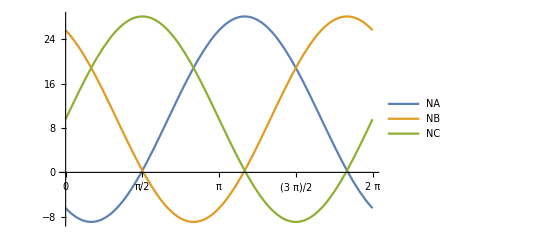

```mathematica
Plot[{NA,NB,NC},{φ,0,2 π},PlotLegends->"Expressions",Ticks->{Range[0,2 Pi,Pi/4],Automatic},PlotRange->Full]
```

Dangerous orientations

```mathematica
DA=(φ/.FindRoot[D[NA,φ]==0,{φ,π/4}]) 180/π
DB=(φ/.FindRoot[D[NB,φ]==0,{φ,3 π/4}]) 180/π
DC=(φ/.FindRoot[D[NC,φ]==0,{φ,6π/4}]) 180/π
```

30.

150.

270.